```mathematica
Get["/home/K/huss/synchrotron/dNsyndEsyn.m"]
```

1.9878×10^-51 GeV^4

```mathematica
nEsyn=201; 
Esynmax=1; (*GeV*)
Esynmin=10^-15;
Esynfac=Exp[Log[Esynmax/Esynmin]/(nEsyn-1)]; 
a1=ParallelTable[{N[Esynmin*Esynfac^(i-1)],dNsyndEsyn[Esynmin*Esynfac^(i-1)]},{i,1,nEsyn}];
```

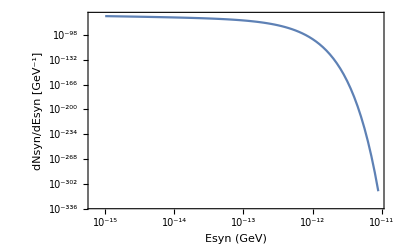

```mathematica
a1pic=ListLogLogPlot[Table[{a1[[i,1]],a1[[i,2]]},{i,1,nEsyn}],Joined->True,Frame->True,FrameLabel->{"Esyn (GeV)","dNsyn/dEsyn [GeV^-1]"}]
```

```mathematica
(*a1=a1/.{Esyn_,0.}:>{Esyn,Exp[-300]};*)
```

```mathematica
Loga1=Table[{Log[a1[[i,1]]],Log[a1[[i,2]]]},{i,1,Length[a1]}];
```

```mathematica
interpLog=Interpolation[Loga1,InterpolationOrder->1];
```

```mathematica
f1[Esyn_]:=Exp[interpLog[Log[Esyn]]]
```

```mathematica
f1pic=LogLogPlot[f1[Esyn],{Esyn,10^-15,1},PlotStyle->Red]
```